```mathematica
gamma[r_,R_]:=(1-3/4*r/R+1/16*(r/R)^3)
```

```mathematica
FullSimplify[ReplaceAll[2*Integrate[4/3*Pi*R^3*gamma[r,R]*r/Sqrt[r^2-z^2],{r,z,2*R}, Assumptions->z>0&&z<2*R],z->xi*2*R],Assumptions->R>0&&xi<2*R]
```

π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
Integrate[gamma[r,R]*4*Pi*r^2,{r,0,2*R}]
```

(4 π R^3)/3

```mathematica
GzSphere:=Integrate[gamma[r,R]4*Pi*r^2,{r,0,2*R}]*2*Integrate[gamma[r,R]*r/Sqrt[r^2-z^2],{r,z,2*R}, Assumptions->z>0&&z<2*R]
```

```mathematica
FullSimplify[ReplaceAll[GzSphere,z->xi*2*R],Assumptions->R>0&&xi<2*R]
```

π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
Simplify[ReplaceAll[GzSphere,z->xi*2*R],Assumptions->x>0&&R>0]
```

π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))])

```mathematica
ISphere[Q_,R_]:=(4/3*Pi*R^3*3(Sin[Q*R]-Q*R*Cos[Q*R])/(Q*R)^3)^2
```

```mathematica
Integrate[(lambda/(2*Pi))^2ISphere[Q,R]*2*Pi*Q,{Q,0,Infinity},Assumptions->R>0]
```

2 lambda^2 π R^4

```mathematica
FullSimplify[Integrate[gamma[r,R]*Sin[Q*r]/(Q*r)*4*Pi*r^2*eta^2*(4/3*Pi*R^3),{r,0,2*R}]]
```

(16 eta^2 π^2 (-Q R Cos[Q R]+Sin[Q R])^2)/Q^6

```mathematica
FullSimplify[Integrate[Exp[-r/xi]*4*Pi*r^2,{r,0,Infinity}],Assumptions->xi>0&&Q>0]
```

8 π xi^3

```mathematica
FullSimplify[Integrate[Exp[-r/xi]*8 π xi^3/1*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}],Assumptions->xi>0&&Q>0]
```

(64 π^2 xi^6)/((1+Q^2 xi^2)^2)

```mathematica
Integrate[2*Exp[-r/xi]*r/Sqrt[r^2-z^2]*8 π xi^3,{r,z,Infinity}, Assumptions->z>0&&xi>0]
```

16 π xi^3 z BesselK[1,z/xi]

```mathematica
Integrate[Exp[-r/xi]/r*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]
```

4 π xi^2

```mathematica
Integrate[gamma[r,R]*4*Pi*r^2,{r,0,2*R}]
```

(4 π R^3)/3

```mathematica
FullSimplify[Normal[Series[u*BesselK[1,u],{u,0,3},Assumptions->u>0]],Assumptions->u>0]
```

1+1/4 u^2 (-1+2 EulerGamma+Log[u^2/4])

```mathematica
Integrate[Exp[-r/xi]*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]
```

8 π xi^3

```mathematica
Simplify[Limit[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H] /(Gamma[2+H]/((H+H^2) Gamma[H])),r->0,Assumptions->a>0 && H>0]]
```

1

```mathematica
Integrate[1/(Gamma[2+H]/((H+H^2) Gamma[H]))*BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*4*pi*r^2,{r,0,Infinity}, Assumptions->z>0&&a>0&&H>-2]
```

(8 a^3 pi √π Gamma[3/2+H])/Gamma[H]

```mathematica
(8 a^3 pi √π Gamma[3/2+1/2])/Gamma[1/2]
```

8 a^3 pi

```mathematica
Integrate[1/((8 a^3 pi √π Gamma[3/2+H])/Gamma[H])/(Gamma[2+H]/((H+H^2) Gamma[H]))*BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*4*pi*r^2*Sin[Q*r]/(Q*r),{r,0,Infinity}, Assumptions->Q>0&&z>0&&a>0&&H>-1/2]
```

(1+a^2 Q^2)^(-3/2-H)

```mathematica
FullSimplify[Gamma[2+H]/((H+H^2) Gamma[H])]
```

1

```mathematica
FullSimplify[Limit[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H],r->0,Assumptions->H>0&&a>0]]
```

1

```mathematica
FullSimplify[2*Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*r/Sqrt[r^2-z^2],{r,z,Infinity}, Assumptions->z>0&&a>0&&H>-2]]
```

(2^(3/2-H) √π (z/a)^H √(a z) BesselK[1/2+H,z/a])/Gamma[H]

```mathematica
GzDABH[z_,a_,H_]:=(2^(3/2-H) √π (z/a)^H √(a z) BesselK[1/2+H,z/a])/Gamma[H]
```

```mathematica
Limit[GzDABH[z,a,H],z->0,Assumptions->a>0&&H>0]
```

(2 a √π Gamma[1/2+H])/Gamma[H]

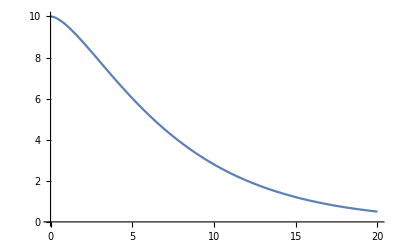

```mathematica
Plot[GzDABH[z,5,1/2],{z,0,20}]
```

```mathematica
FullSimplify[(2^(-5/2-H) (z/u)^(-5/2-H) z^(1/2+H) BesselK[1/2+H,z/(z/u)])/(π Gamma[3/2+H]),Assumptions->H>0&&u>0&&z>0]
```

(2^(-5/2-H) u^(5/2+H) BesselK[1/2+H,u])/(π z^2 Gamma[3/2+H])

```mathematica
FunctionExpand[Normal[Assuming[H>0&&a>0,Series[(2^(-5/2-H) u^(5/2+H) BesselK[1/2+H,u])/(π z^2 Gamma[3/2+H]),{u,0,3}]]]]
```

u^2/(4 (1+2 H) π z^2)-u^4/(8 (-1+2 H) (1+2 H) π z^2)-(2^(-6-2 H) u^(5+2 H) Gamma[-3/2-H])/(π z^2 Gamma[3/2+H])+(2^(-4-2 H) u^(3+2 H) Gamma[-1/2-H])/(π z^2 Gamma[3/2+H])

```mathematica
Assuming[H>0,Limit[(u/2)^(1/2+H)*BesselK[1/2+H,u],u->0]]
```

1/2 Gamma[1/2+H]

```mathematica
Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]/((8 a^3 π^(3/2) Gamma[3/2+H])/Gamma[H])*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}, Assumptions->Q>0&&a>0&&H>-3/2]
```

(1+a^2 Q^2)^(-3/2-H)

```mathematica
FullSimplify[Integrate[BesselK[H,r/a]*(r/(2*a))^H*2/Gamma[H]*((8 a^3 π^(3/2) Gamma[3/2+H])/Gamma[H])*4*Pi*r^2,{r,0,Infinity}, Assumptions->Q>0&&a>0&&H>-3]]
```

(64 a^6 π^3 Gamma[3/2+H]^2)/Gamma[H]^2